```mathematica
O1=({{2, 4}, {1, 3}, {0, 0}, {0, 0}})
```

{{2,4},{1,3},{0,0},{0,0}}

```mathematica
SingularValueDecomposition[O1]
```

{{{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{0,0,0,1},{0,0,1,0}},{{√(15+√221),0},{0,√(15-√221)},{0,0},{0,0}},{{(-10+√221)/(11 √(1+1/121 (-10+√221)^2)),(-10-√221)/(11 √(1+1/121 (-10-√221)^2))},{1/(√(1+1/121 (-10+√221)^2)),1/(√(1+1/121 (-10-√221)^2))}}}

```mathematica
{u, σ, v} = SingularValueDecomposition[O1*Transpose[O1]]
```

Thread::tdlen: {{2,4},{1,3},{0,0},{0,0}} {{2,1,0,0},{4,3,0,0}} 中长度不相等的对象无法合并.

Set::shape: 列表 {u,σ,v} 和 SingularValueDecomposition[{{2,1,0,0},{4,3,0,0}} {{2,4},{1,3},{0,0},{0,0}}] 形状不同.

SingularValueDecomposition[{{2,1,0,0},{4,3,0,0}} {{2,4},{1,3},{0,0},{0,0}}]

```mathematica
MatrixForm/@{u,σ,v}
```

{((4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(√(15+√221) | 0
0 | √(15-√221)
0 | 0
0 | 0),((-10+√221)/(11 √(1+1/121 (-10+√221)^2)) | (-10-√221)/(11 √(1+1/121 (-10-√221)^2))
1/(√(1+1/121 (-10+√221)^2)) | 1/(√(1+1/121 (-10-√221)^2)))}

```mathematica
(*Define the matrix O*)O1={{2,4},{1,3},{0,0},{0,0}}

(*Step 1:Calculate OO†*)
OOt=O1.ConjugateTranspose[O1]

(*Step 2:Calculate O†O*)
OtO=ConjugateTranspose[O1].O1

(*Step 3:Find eigenvalues and eigenvectors of OO†*)
{eigenvalsOOt,eigenvecOOt}=Eigensystem[OOt]

(*Step 4:Find eigenvalues and eigenvectors of O†O*)
{eigenvalsOtO,eigenvecOtO}=Eigensystem[OtO]

(*Step 5:Calculate singular values*)
singularValues=Sqrt[eigenvalsOOt]

(*Step 6:Normalize eigenvectors of OO† to get U*)
U=Normalize/@eigenvecOOt

(*Step 7:Normalize eigenvectors of O†O to get V*)
V=Normalize/@eigenvecOtO

(*Step 8:Conjugate transpose V to get V†*)
Vdagger=ConjugateTranspose[V]

(*Display results*)
Print["Singular Values:"]
singularValues//MatrixForm

Print["Left Singular Vectors (U):"]
U//MatrixForm

Print["Right Singular Vectors (V†):"]
Vdagger//MatrixForm
```

{{2,4},{1,3},{0,0},{0,0}}

{{20,14,0,0},{14,10,0,0},{0,0,0,0},{0,0,0,0}}

{{5,11},{11,25}}

{{15+√221,15-√221,0,0},{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}}

{{15+√221,15-√221},{{1/11 (-10+√221),1},{1/11 (-10-√221),1}}}

{√(15+√221),√(15-√221),0,0}

{{(5+√221)/(14 √(1+1/196 (5+√221)^2)),1/(√(1+1/196 (5+√221)^2)),0,0},{(5-√221)/(14 √(1+1/196 (-5+√221)^2)),1/(√(1+1/196 (-5+√221)^2)),0,0},{0,0,0,1},{0,0,1,0}}

{{(-10+√221)/(11 √(1+1/121 (-10+√221)^2)),1/(√(1+1/121 (-10+√221)^2))},{(-10-√221)/(11 √(1+1/121 (10+√221)^2)),1/(√(1+1/121 (10+√221)^2))}}

{{(-10+√221)/(11 √(1+1/121 (-10+√221)^2)),(-10-√221)/(11 √(1+1/121 (10+√221)^2))},{1/(√(1+1/121 (-10+√221)^2)),1/(√(1+1/121 (10+√221)^2))}}

Singular Values:

(√(15+√221)
√(15-√221)
0
0)

Left Singular Vectors (U):

((5+√221)/(14 √(1+1/196 (5+√221)^2)) | 1/(√(1+1/196 (5+√221)^2)) | 0 | 0
(5-√221)/(14 √(1+1/196 (-5+√221)^2)) | 1/(√(1+1/196 (-5+√221)^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Right Singular Vectors (V†):

((-10+√221)/(11 √(1+1/121 (-10+√221)^2)) | (-10-√221)/(11 √(1+1/121 (10+√221)^2))
1/(√(1+1/121 (-10+√221)^2)) | 1/(√(1+1/121 (10+√221)^2)))

```mathematica
√(15+√221)
```

√(15+√221)

```mathematica
N[√(15+√221)]
```

5.46499

```mathematica
√(15-√221)
```

√(15-√221)

```mathematica
N[√(15-√221)]
```

0.365966

```mathematica
(5-√221)/(14 √(1+1/196 (-5+√221)^2))
```

(5-√221)/(14 √(1+1/196 (-5+√221)^2))

```mathematica
N[(5-√221)/(14 √(1+1/196 (-5+√221)^2))]
```

-0.576048

```mathematica
O1
```

{{2,4},{1,3},{0,0},{0,0}}

```mathematica
MatrixForm[{{2,4},{1,3},{0,0},{0,0}}]
```

(2 | 4
1 | 3
0 | 0
0 | 0)

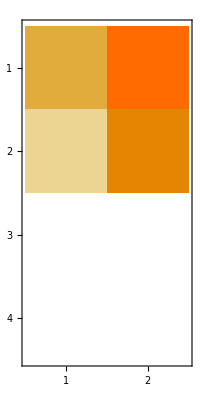

```mathematica
MatrixPlot[{{2,4},{1,3},{0,0},{0,0}}]
```

```mathematica
OtO=ConjugateTranspose[O1].O1
```

{{5,11},{11,25}}

```mathematica
MatrixForm[OtO]
```

(5 | 11
11 | 25)

```mathematica
aa=O1.ConjugateTranspose[O1]
```

{{20,14,0,0},{14,10,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[aa]
```

(20 | 14 | 0 | 0
14 | 10 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
{a,b}=Eigensystem[aa]
```

{{15+√221,15-√221,0,0},{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}}

```mathematica
MatrixForm[a]
```

(15+√221
15-√221
0
0)

```mathematica
DiagonalMatrix[a]
```

{{15+√221,0,0,0},{0,15-√221,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[{{15+√221,0,0,0},{0,15-√221,0,0},{0,0,0,0},{0,0,0,0}}]
```

(15+√221 | 0 | 0 | 0
0 | 15-√221 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
a1=DiagonalMatrix[a];
```

```mathematica
MatrixForm[{{15+√221,0,0,0},{0,15-√221,0,0},{0,0,0,0},{0,0,0,0}}]
```

(15+√221 | 0 | 0 | 0
0 | 15-√221 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
b
```

{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}]
```

(1/14 (5+√221) | 1 | 0 | 0
1/14 (5-√221) | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
b.a1.Transpose[b]
```

{{15-√221+1/196 (5+√221)^2 (15+√221),15-√221+1/196 (5-√221) (5+√221) (15+√221),0,0},{15-√221+1/196 (5-√221) (5+√221) (15+√221),15-√221+1/196 (5-√221)^2 (15+√221),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[%75]
```

(15-√221+1/196 (5+√221)^2 (15+√221) | 15-√221+1/196 (5-√221) (5+√221) (15+√221) | 0 | 0
15-√221+1/196 (5-√221) (5+√221) (15+√221) | 15-√221+1/196 (5-√221)^2 (15+√221) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
15-√221+1/196 (5+√221)^2 (15+√221)
```

15-√221+1/196 (5+√221)^2 (15+√221)

```mathematica
N[15-√221+1/196 (5+√221)^2 (15+√221)]
```

60.2715

```mathematica
1/14 (5+√221)
```

1/14 (5+√221)

```mathematica
N[1/14 (5+√221)]
```

1.419

```mathematica
(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))
```

(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))

```mathematica
N[(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))]
```

0.817416

```mathematica
(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2))
```

(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2))

```mathematica
N[(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2))]
```

-0.576048

```mathematica
(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))
```

(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))

```mathematica
N[(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))]
```

0.576048

```mathematica
(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2))==(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))
```

False

```mathematica
{{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0}}
```

{{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0}}

```mathematica
MatrixForm[%88]
```

((4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0)

```mathematica
{{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{0,0,0,1},{0,0,1,0}}
```

```mathematica
ooi={{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{0,0,0,1},{0,0,1,0}}
```

{{(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)),(3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)),0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[ooi]
```

((4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
ooi.a1.Transpose[ooi]
```

{{((15-√221) (4+2/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (4+2/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2),((15-√221) (3+1/11 (-10-√221)) (4+2/11 (-10-√221)))/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221)) (4+2/11 (-10+√221)))/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2),0,0},{((15-√221) (3+1/11 (-10-√221)) (4+2/11 (-10-√221)))/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221)) (4+2/11 (-10+√221)))/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2),((15-√221) (3+1/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[%94]
```

(((15-√221) (4+2/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (4+2/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2) | ((15-√221) (3+1/11 (-10-√221)) (4+2/11 (-10-√221)))/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221)) (4+2/11 (-10+√221)))/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2) | 0 | 0
((15-√221) (3+1/11 (-10-√221)) (4+2/11 (-10-√221)))/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221)) (4+2/11 (-10+√221)))/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2) | ((15-√221) (3+1/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (3+1/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
((15-√221) (4+2/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (4+2/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)
```

((15-√221) (4+2/11 (-10-√221))^2)/((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)+((15+√221) (4+2/11 (-10+√221))^2)/((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)

```mathematica
N[%96]
```

20.

```mathematica
Simplify[(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))]
```

(12+√221) √(2/(1105+71 √221))

```mathematica
RootReduce[(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))]
```

```mathematica
Simplify[ooi]
```

{{(12+√221) √(2/(1105+71 √221)),-√(2/(1105-71 √221)) (-12+√221),0,0},{(23+√221)/(√(2210+142 √221)),(23-√221)/(√(2210-142 √221)),0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[{{(12+√221) √(2/(1105+71 √221)),-√(2/(1105-71 √221)) (-12+√221),0,0},{(23+√221)/(√(2210+142 √221)),(23-√221)/(√(2210-142 √221)),0,0},{0,0,0,1},{0,0,1,0}}]
```

((12+√221) √(2/(1105+71 √221)) | -√(2/(1105-71 √221)) (-12+√221) | 0 | 0
(23+√221)/(√(2210+142 √221)) | (23-√221)/(√(2210-142 √221)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Eigensystem[({{5, 11}, {11, 25}})]
```

{{15+√221,15-√221},{{1/11 (-10+√221),1},{1/11 (-10-√221),1}}}

```mathematica
vv={{1/11 (-10+√221),1},{1/11 (-10-√221),1}};
```

```mathematica
MatrixForm[{{1/11 (-10+√221),1},{1/11 (-10-√221),1}}]
```

```mathematica
({{1/11 (-10+√221), 1}, {1/11 (-10-√221), 1}})
```

{{1/11 (-10+√221),1},{1/11 (-10-√221),1}}

```mathematica
Eigensystem[{{20,14,0,0},{14,10,0,0},{0,0,0,0},{0,0,0,0}}]
```

{{15+√221,15-√221,0,0},{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}}

```mathematica
uu={{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}
```

{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[uu]
```

(1/14 (5+√221) | 1 | 0 | 0
1/14 (5-√221) | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
s=DiagonalMatrix[{Sqrt[15+√221],Sqrt[15-√221],0,0}]
```

{{√(15+√221),0,0,0},{0,√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[s]
```

(√(15+√221) | 0 | 0 | 0
0 | √(15-√221) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[{{15+√221,0,0,0},{0,15-√221,0,0},{0,0,0,0},{0,0,0,0}}]
```

(15+√221 | 0 | 0 | 0
0 | 15-√221 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
O1=uu.s.Transpose[vv]
```

Dot::dotsh: 张量 {{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}} 和 {{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} 含有不兼容形状.

{{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}.{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}}

```mathematica
Simplify[%123]
```

{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}} {{√(15+√221),0,0,0},{0,√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[%120]
```

{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}} {{√(15+√221),0,0,0},{0,√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FunctionDomain[%121,{}]
```

True

```mathematica
MatrixForm[O1]
```

{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}} {{√(15+√221),0,0,0},{0,√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
uu1=({{0, 0, 1/14 (5+√221), 1/14 (5-√221)}, {0, 0, 1, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}});
```

```mathematica
s={{0,0,0,0},{0,0,0,0},{0,0,√(15-√221),0},{0,0,0,√(15+√221)}};
```

```mathematica
MatrixForm[{{0,0,0,0},{0,0,0,0},{0,0,√(15-√221),0},{0,0,0,√(15+√221)}}]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | √(15-√221) | 0
0 | 0 | 0 | √(15+√221))

```mathematica
vv1=({{1/11 (-10-√221), 1/11 (-10+√221)}, {1, 1}});
```

```mathematica
{{1/11 (-10-√221),1/11 (-10+√221)},{1,1}}
```

{{-11/(2 √221),-(10-√221)/(2 √221)},{11/(2 √221),-(-10-√221)/(2 √221)}}

```mathematica
MatrixForm[{{-11/(2 √221),-(10-√221)/(2 √221)},{11/(2 √221),-(-10-√221)/(2 √221)}}]
```

(-11/(2 √221) | -(10-√221)/(2 √221)
11/(2 √221) | -(-10-√221)/(2 √221))

```mathematica
oi=({{0, 0, 1/14 (5+√221), 1/14 (5-√221)}, {0, 0, 1, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}})({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, √(15+√221), 0}, {0, 0, 0, √(15-√221)}})({{-11/(2 √221), -(10-√221)/(2 √221)}, {11/(2 √221), -(-10-√221)/(2 √221)}})
```

Thread::tdlen: {{0,0,1/14 (5+√221),1/14 (5-√221)},{0,0,1,1},{0,1,0,0},{1,0,0,0}} {{0,0,0,0},{0,0,0,0},{0,0,√(15+√221),0},{0,0,0,√(15-√221)}} {{-11/(2 √221),-(10-√221)/(2 √221)},{11/(2 √221),-(-10-√221)/(2 √221)}} 中长度不相等的对象无法合并.

{{-11/(2 √221),-(10-√221)/(2 √221)},{11/(2 √221),-(-10-√221)/(2 √221)}} {{0,0,0,0},{0,0,0,0},{0,0,√(15+√221),0},{0,0,0,√(15-√221)}} {{0,0,1/14 (5+√221),1/14 (5-√221)},{0,0,1,1},{0,1,0,0},{1,0,0,0}}

```mathematica
Simplify[oi]
```

{{0,0,1/14 (5+√221),1/14 (5-√221)},{0,0,1,1},{0,1,0,0},{1,0,0,0}}

```mathematica
MatrixForm[{{0,0,1/14 (5+√221),1/14 (5-√221)},{0,0,1,1},{0,1,0,0},{1,0,0,0}}]
```

(0 | 0 | 1/14 (5+√221) | 1/14 (5-√221)
0 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
SingularValueDecomposition[O1]
```

SingularValueDecomposition[{{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}.{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}}]

```mathematica
{u, σ, v} = SingularValueDecomposition[O1.Transpose[O1]]
```

Dot::dotsh: 张量 {{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}} 和 {{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} 含有不兼容形状.

Set::shape: 列表 {u,σ,v} 和 SingularValueDecomposition[{{1/14 (5+√221) √(15+Power[«2»]),√(15-Power[«2»]),0,0},{1/14 (5-Power[«2»]) √(15+Power[«2»]),√(15-Power[«2»]),0,0},{0,0,0,0},{0,0,0,0}}.{{1/11 (-10+√221),1/11 (-10-Power[«2»])},{1,1}}.(] 形状不同.

SingularValueDecomposition[{{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}.{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}}.Transpose[({{1/14 (5+√221) √(15+√221),√(15-√221),0,0},{1/14 (5-√221) √(15+√221),√(15-√221),0,0},{0,0,0,0},{0,0,0,0}}.{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}})]]

```mathematica
MatrixForm/@{u,σ,v}
```

{((4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (4+2/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
(3+1/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2)) | (3+1/11 (-10-√221))/(√((3+1/11 (-10-√221))^2+(4+2/11 (-10-√221))^2)) | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(√(15+√221) | 0
0 | √(15-√221)
0 | 0
0 | 0),((-10+√221)/(11 √(1+1/121 (-10+√221)^2)) | (-10-√221)/(11 √(1+1/121 (-10-√221)^2))
1/(√(1+1/121 (-10+√221)^2)) | 1/(√(1+1/121 (-10-√221)^2)))}

```mathematica
uu=({{0, 0, 1/14 (5+√221), 1/14 (5-√221)}, {0, 0, 1, 1}, {0, 1, 0, 0}, {1, 0, 0, 0}})
```

{{0,0,1/14 (5+√221),1/14 (5-√221)},{0,0,1,1},{0,1,0,0},{1,0,0,0}}

```mathematica
vv={{1/11 (-10+√221),1/11 (-10-√221)},{1,1}}
```

{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}}

```mathematica
MatrixForm[vv]
```

(1/11 (-10+√221) | 1/11 (-10-√221)
1 | 1)

```mathematica
ss=({{√(15-√221), 0}, {0, √(15+√221)}, {0, 0}, {0, 0}});
```

```mathematica
MatrixForm[{{√(15-√221),0},{0,√(15+√221)},{0,0},{0,0}}]
```

(√(15-√221) | 0
0 | √(15+√221)
0 | 0
0 | 0)

```mathematica
uu.ss.Transpose[vv]
```

{{0,0},{0,0},{1/11 (-10-√221) √(15+√221),√(15+√221)},{1/11 √(15-√221) (-10+√221),√(15-√221)}}

```mathematica
MatrixForm[{{0,0},{0,0},{1/11 (-10-√221) √(15+√221),√(15+√221)},{1/11 √(15-√221) (-10+√221),√(15-√221)}}]
```

(0 | 0
0 | 0
1/11 (-10-√221) √(15+√221) | √(15+√221)
1/11 √(15-√221) (-10+√221) | √(15-√221))

```mathematica
MatrixForm[{{0,0},{0,0},{1/11 (-10-√221) √(15-√221),√(15-√221)},{1/11 (-10+√221) √(15+√221),√(15+√221)}}]
```

(0 | 0
0 | 0
1/11 (-10-√221) √(15-√221) | √(15-√221)
1/11 (-10+√221) √(15+√221) | √(15+√221))

```mathematica
1/11 (-15-√221) √(15+√221)
```

1/11 (-15-√221) √(15+√221)

```mathematica
Abs[1/11 (-15-√221) √(15+√221)]
```

1/11 (15+√221)^(3/2)

```mathematica
N[1/11 (-10-√221) √(15+√221)]
```

-12.3539

```mathematica
({{1/14 (5+√221), 1, 0, 0}, {1/14 (5-√221), 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}).({{√(15+√221), 0}, {0, √(15-√221)}, {0, 0}, {0, 0}}).ConjugateTranspose[({{1/11 (-10+√221), 1}, {1/11 (-10-√221), 1}})]
```

{{√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221),√(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)},{√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221),√(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)},{0,0},{0,0}}

```mathematica
MatrixForm[%205]
```

(√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)
√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)
0 | 0
0 | 0)

```mathematica
MatrixForm[%200]
```

((11 √(15-√221))/(-10-√221)+(11 (5+√221) √(15+√221))/(14 (-10+√221)) | √(15-√221)+1/14 (5+√221) √(15+√221)
(11 √(15-√221))/(-10-√221)+(11 (5-√221) √(15+√221))/(14 (-10+√221)) | √(15-√221)+1/14 (5-√221) √(15+√221)
0 | 0
0 | 0)

```mathematica
MatrixForm[%188]
```

(√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)
√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)
0 | 0
0 | 0)

```mathematica
MatrixForm[%184]
```

(1/154 √(15-√221) (-10+√221) (5+√221)+√(15+√221) | 1/154 (-10-√221) √(15-√221) (5+√221)+√(15+√221)
1/154 (5-√221) √(15-√221) (-10+√221)+√(15+√221) | 1/154 (-10-√221) (5-√221) √(15-√221)+√(15+√221)
0 | 0
0 | 0)

```mathematica
MatrixForm[{{0,0},{0,0},{√(15+√221),√(15+√221)},{1/11 √(15-√221) (-10+√221),1/11 (-10-√221) √(15-√221)}}]
```

(0 | 0
0 | 0
√(15+√221) | √(15+√221)
1/11 √(15-√221) (-10+√221) | 1/11 (-10-√221) √(15-√221))

```mathematica
First[{{0,0},{0,0},{√(15+√221),√(15+√221)},{1/11 √(15-√221) (-10+√221),1/11 (-10-√221) √(15-√221)}}]
```

{0,0}

```mathematica
Simplify[{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{√(15+√221),0},{0,√(15-√221)},{0,0},{0,0}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}]
```

Thread::tdlen: {{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{√(15+√221),0},{0,√(15-√221)},{0,0},{0,0}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}} 中长度不相等的对象无法合并.

{{1/11 (-10+√221),1/11 (-10-√221)},{1,1}} {{√(15+√221),0},{0,√(15-√221)},{0,0},{0,0}} {{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
1/154 √(15-√221) (-10+√221) (5+√221)+√(15+√221)
```

1/154 √(15-√221) (-10+√221) (5+√221)+√(15+√221)

```mathematica
N[1/154 √(15-√221) (-10+√221) (5+√221)+√(15+√221)]
```

5.69471

```mathematica
√(15-√221)+1/154 (-10+√221) (5+√221)
```

√(15-√221)+1/154 (-10+√221) (5+√221)

```mathematica
N[√(15-√221)+1/154 (-10+√221) (5+√221)]
```

0.993691

```mathematica
uu.({{√(15+√221), 0}, {0, √(15-√221)}, {0, 0}, {0, 0}}).Transpose[({{1/11 (-10+√221), 1}, {1/11 (-10-√221), 1}})]
```

{{0,0},{0,0},{√(15-√221),√(15-√221)},{1/11 (-10+√221) √(15+√221),1/11 (-10-√221) √(15+√221)}}

```mathematica
MatrixForm[{{0,0},{0,0},{√(15-√221),√(15-√221)},{1/11 (-10+√221) √(15+√221),1/11 (-10-√221) √(15+√221)}}]
```

(0 | 0
0 | 0
√(15-√221) | √(15-√221)
1/11 (-10+√221) √(15+√221) | 1/11 (-10-√221) √(15+√221))

```mathematica
({{1/14 (5+√221), 1, 0, 0}, {1/14 (5-√221), 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}).({{√(15+√221), 0}, {0, √(15-√221)}, {0, 0}, {0, 0}}).Transpose[vv]
```

{{1/11 (-10-√221) √(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221),√(15-√221)+1/14 (5+√221) √(15+√221)},{1/11 (-10-√221) √(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221),√(15-√221)+1/14 (5-√221) √(15+√221)},{0,0},{0,0}}

```mathematica
MatrixForm[%194]
```

```mathematica
({{1/11 (-10-√221) √(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221), √(15-√221)+1/14 (5+√221) √(15+√221)}, {1/11 (-10-√221) √(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221), √(15-√221)+1/14 (5-√221) √(15+√221)}, {0, 0}, {0, 0}})
```

{{1/11 (-10-√221) √(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221),√(15-√221)+1/14 (5+√221) √(15+√221)},{1/11 (-10-√221) √(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221),√(15-√221)+1/14 (5-√221) √(15+√221)},{0,0},{0,0}}

```mathematica
Transpose[%198]
```

{{1/11 (-10-√221) √(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221),1/11 (-10-√221) √(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221),0,0},{√(15-√221)+1/14 (5+√221) √(15+√221),√(15-√221)+1/14 (5-√221) √(15+√221),0,0}}

```mathematica
1/11 (-10-√221) √(15-√221)+1/154 (-10+√221)
```

1/11 (-10-√221) √(15-√221)+1/154 (-10+√221)

```mathematica
N[1/11 (-10-√221) √(15-√221)+1/154 (-10+√221)]
```

-0.795688

```mathematica
(11 √(15-√221))/(-10-√221)+(11 (5+√221) √(15+√221))/(14 (-10+√221))
```

(11 √(15-√221))/(-10-√221)+(11 (5+√221) √(15+√221))/(14 (-10+√221))

```mathematica
RootReduce[(11 √(15-√221))/(-10-√221)+(11 (5+√221) √(15+√221))/(14 (-10+√221))]
```

```mathematica
N[Root[33641429056-327934200 #1^2+717409 #1^4&,4,0]]
```

17.3683

```mathematica
√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)
```

√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)

```mathematica
N[√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)]
```

3.79647

```mathematica
({{1/14 (5+√221), 1, 0, 0}, {1/14 (5-√221), 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}).({{√(15+√221), 0}, {0, √(15-√221)}, {0, 0}, {0, 0}}).ConjugateTranspose[({{1/11 (-10+√221), 1}, {1/11 (-10-√221), 1}})]
```

{{√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221),√(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)},{√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221),√(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)},{0,0},{0,0}}

```mathematica
MatrixForm[%209]
```

(√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)
√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)
0 | 0
0 | 0)

```mathematica
TableForm[%209]
```

√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5+√221) √(15+√221)
√(15-√221)+1/154 (5-√221) (-10+√221) √(15+√221) | √(15-√221)+1/154 (-10-√221) (5-√221) √(15+√221)
0 | 0
0 | 0

```mathematica
(4+2/11 (-10+√221))/(√((3+1/11 (-10+√221))^2+(4+2/11 (-10+√221))^2))==1/14 (5+√221)
```

False

```mathematica
{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}
```

{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[{{1/14 (5+√221),1,0,0},{1/14 (5-√221),1,0,0},{0,0,0,1},{0,0,1,0}}]
```

(1/14 (5+√221) | 1 | 0 | 0
1/14 (5-√221) | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)
```

√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)

```mathematica
N[√(15-√221)+1/154 (-10+√221) (5+√221) √(15+√221)]
```

3.79647